```mathematica
fac=2;
vel=2;
ϕ=1;
μw=1;
μo=1;
krw[sw_]=sw^fac;
kro[sw_]=(1-sw)^fac;
Plot[{krw[sw],kro[sw]},{sw,0,1}];λw[sw_]=krw[sw]/μw;
λo[sw_]=kro[sw]/μo;
Plot[{λw[sw],λo[sw]},{sw,0,1}];

fw[sw_]=λw[sw]/(λw[sw]+λo[sw]);
Plot[fw[sw],{sw,0,1},PlotRange->{{0,1},{0,1}}];
pontsfw=Table[{sw,fw[sw]/sw},{sw,0.001,1,0.001}];
maxderiv=Max[pontsfw];
FindGabriel[val_,vector_]:=Block[{fval=val,fvector=vector},
nVals= Length[fvector];
For[i=1,i<=nVals, i++,
If[fvector[[i,2]]==fval,
Return[fvector[[i,1]]];
];
];
];
Swf=FindGabriel[maxderiv,pontsfw]
dfwdsw[sw_]=D[fw[sw],sw];
x[sw_,time_]=(vel/ϕ)dfwdsw[sw]*time;
```

0.707

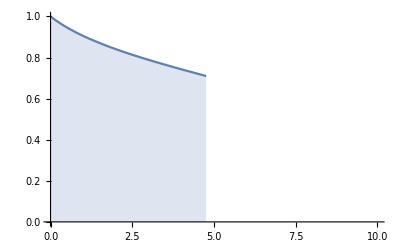

```mathematica
points=Table[{x[sw,2],sw},{sw,1,Swf,-0.01}];
ListPlot[points,Joined->True,PlotRange->{{0,10},{0,1}},Filling->Axis]
```